Parameter initialization

```mathematica
kk=1.01*^-6 ; (*spring constant*)
zeta=2.02*^-6; (*friction coefficient*)
LL=10*^-9; (*contact distance*)
kbT=1.38*^-23*300; 
kappa=kk*LL^2/2/kbT; (*dimensionless trap stiffness*)
DD=kbT/zeta; (*diffusion coefficient*)
mmax=50(*number of terms kept in the series solution*)
```

1.01×10^-6

2.02×10^-6

1/100000000

4.14×10^-21

0.0121981

2.0495×10^-15

50

Calculate (first argument) zeros of the Tricomi function

```mathematica
aaZeros[n_,b_,k_]=(-n - 2/π*Sqrt[k*n]-2k/Pi^2+b/2+1/4+(k^2(1/3-4/π^2)+k-(b-1)^2+1/4)/4/π/Sqrt[k*n])(*Estimate for zeros, given by https://dlmf.nist.gov/13.9*)
Clear[zeros]
zeros[κ_]:=zeros[κ]=λ/. Table[FindRoot[HypergeometricU[-λ,3/2,κ]*κ^λ,{λ,-aaZeros[m,3/2,κ]}],{m,1,mmax}]; (* the asymptotic behavior of U is κ^(-λ)so the κ^λ-term removes that behavior *)
myzeros=zeros[kappa]
Table[HypergeometricU[-zeros[kappa][[m]],3/2,kappa],{m,1,mmax}]
```

1/4+b/2-n-(2 k)/π^2-(2 √(k n))/π+(1/4-(-1+b)^2+k+k^2 (1/3-4/π^2))/(4 √(k n) π)

{0.0647093,1.09592,2.1193,3.13878,4.15582,5.17115,6.18521,7.19826,8.2105,9.22206,10.233,11.2435,12.2536,13.2632,14.2725,15.2815,16.2903,17.2987,18.3069,19.315,20.3228,21.3304,22.3378,23.3451,24.3523,25.3593,26.3661,27.3729,28.3795,29.386,30.3924,31.3987,32.4049,33.411,34.417,35.4229,36.4287,37.4345,38.4402,39.4458,40.4513,41.4568,42.4622,43.4675,44.4728,45.4781,46.4832,47.4883,48.4934,49.4984}

{-8.04171×10^-18,5.64216×10^-16,7.32899×10^-14,1.68314×10^-13,-5.31004×10^-13,2.43362×10^-12,-1.12993×10^-11,-4.12961×10^-12,-3.22755×10^-10,7.6425×10^-9,7.10828×10^-8,-3.49338×10^-7,-8.54804×10^-6,0.000162955,-0.00146302,0.0307545,-0.566753,-16.577,-191.11,-6090.35,-88383.1,-3.81026×10^6,7.81672×10^7,3.2512×10^8,-9.56869×10^9,-1.22028×10^12,7.90799×10^12,-4.44312×10^14,-1.72844×10^16,7.33399×10^17,2.49016×10^19,1.03948×10^20,-3.95587×10^22,1.39007×10^24,5.59683×10^25,-1.4797×10^27,9.3498×10^28,-1.41822×10^30,-1.00871×10^32,5.27602×10^33,3.68927×10^34,-1.00912×10^37,2.71966×10^38,-5.18826×10^39,-3.19423×10^41,1.67947×10^43,1.96523×10^45,-8.61059×10^46,-6.16815×10^47,1.7757×10^50}

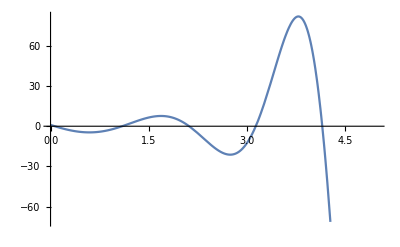

```mathematica
Plot[HypergeometricU[-λ,3/2,kappa],{λ,0 ,5}](*Visualize the first few zeros given kappa*)
```

Calculate the normalized Tricomi function (as orthonormal eigenfunction bases)

```mathematica
norms[κ_]:=norms[κ]=Table[NIntegrate[z^2*Exp[-κ*z^2]*(HypergeometricU[-zeros[κ][[m]],3/2,κ*z^2])^2,{z,1,∞},Method->"GlobalAdaptive",MaxRecursion->10],{m,1,mmax}];
myeigenfunctions[κ_]:=myeigenfunctions[κ]=Table[HypergeometricU[-zeros[κ][[m]],3/2,κ*z^2]/Sqrt[norms[κ][[m]]],{m,1,mmax}];
```

```mathematica
myefs=myeigenfunctions[kappa] (* my normalized eigenfunctions *)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in z near {z} = {63.033}. NIntegrate obtained 3.44872×10^43 and 2.42311×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in z near {z} = {76.1722}. NIntegrate obtained 3.45826×10^57 and 7.13123×10^51 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in z near {z} = {84.7868}. NIntegrate obtained 2.22598×10^72 and 2.43397×10^70 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0570292 HypergeometricU[-0.0647093,3/2,0.0121981 z^2],0.0430992 HypergeometricU[-1.09592,3/2,0.0121981 z^2],0.0179834 HypergeometricU[-2.1193,3/2,0.0121981 z^2],0.00520502 HypergeometricU[-3.13878,3/2,0.0121981 z^2],0.00115504 HypergeometricU[-4.15582,3/2,0.0121981 z^2],0.000207994 HypergeometricU[-5.17115,3/2,0.0121981 z^2],0.000031529 HypergeometricU[-6.18521,3/2,0.0121981 z^2],4.12783×10^-6 HypergeometricU[-7.19826,3/2,0.0121981 z^2],4.75702×10^-7 HypergeometricU[-8.2105,3/2,0.0121981 z^2],4.89664×10^-8 HypergeometricU[-9.22206,3/2,0.0121981 z^2],4.5546×10^-9 HypergeometricU[-10.233,3/2,0.0121981 z^2],3.86448×10^-10 HypergeometricU[-11.2435,3/2,0.0121981 z^2],3.01452×10^-11 HypergeometricU[-12.2536,3/2,0.0121981 z^2],2.17618×10^-12 HypergeometricU[-13.2632,3/2,0.0121981 z^2],1.46207×10^-13 HypergeometricU[-14.2725,3/2,0.0121981 z^2],9.18654×10^-15 HypergeometricU[-15.2815,3/2,0.0121981 z^2],5.42116×10^-16 HypergeometricU[-16.2903,3/2,0.0121981 z^2],3.01588×10^-17 HypergeometricU[-17.2987,3/2,0.0121981 z^2],1.58693×10^-18 HypergeometricU[-18.3069,3/2,0.0121981 z^2],7.92161×10^-20 HypergeometricU[-19.315,3/2,0.0121981 z^2],3.76128×10^-21 HypergeometricU[-20.3228,3/2,0.0121981 z^2],1.70283×10^-22 HypergeometricU[-21.3304,3/2,0.0121981 z^2],7.36664×10^-24 HypergeometricU[-22.3378,3/2,0.0121981 z^2],3.05139×10^-25 HypergeometricU[-23.3451,3/2,0.0121981 z^2],1.2124×10^-26 HypergeometricU[-24.3523,3/2,0.0121981 z^2],4.62857×10^-28 HypergeometricU[-25.3593,3/2,0.0121981 z^2],1.70048×10^-29 HypergeometricU[-26.3661,3/2,0.0121981 z^2],6.02062×10^-31 HypergeometricU[-27.3729,3/2,0.0121981 z^2],2.057×10^-32 HypergeometricU[-28.3795,3/2,0.0121981 z^2],6.79028×10^-34 HypergeometricU[-29.386,3/2,0.0121981 z^2],2.16822×10^-35 HypergeometricU[-30.3924,3/2,0.0121981 z^2],6.70253×10^-37 HypergeometricU[-31.3987,3/2,0.0121981 z^2],2.00938×10^-38 HypergeometricU[-32.4049,3/2,0.0121981 z^2],5.84328×10^-40 HypergeometricU[-33.411,3/2,0.0121981 z^2],1.65014×10^-41 HypergeometricU[-34.417,3/2,0.0121981 z^2],4.52919×10^-43 HypergeometricU[-35.4229,3/2,0.0121981 z^2],1.2092×10^-44 HypergeometricU[-36.4287,3/2,0.0121981 z^2],3.14257×10^-46 HypergeometricU[-37.4345,3/2,0.0121981 z^2],8.08137×10^-48 HypergeometricU[-38.4402,3/2,0.0121981 z^2],1.96333×10^-49 HypergeometricU[-39.4458,3/2,0.0121981 z^2],4.72595×10^-51 HypergeometricU[-40.4513,3/2,0.0121981 z^2],1.11029×10^-52 HypergeometricU[-41.4568,3/2,0.0121981 z^2],2.54734×10^-54 HypergeometricU[-42.4622,3/2,0.0121981 z^2],5.7106×10^-56 HypergeometricU[-43.4675,3/2,0.0121981 z^2],1.25155×10^-57 HypergeometricU[-44.4728,3/2,0.0121981 z^2],2.68293×10^-59 HypergeometricU[-45.4781,3/2,0.0121981 z^2],5.62822×10^-61 HypergeometricU[-46.4832,3/2,0.0121981 z^2],1.15594×10^-62 HypergeometricU[-47.4883,3/2,0.0121981 z^2],2.32538×10^-64 HypergeometricU[-48.4934,3/2,0.0121981 z^2],4.58386×10^-66 HypergeometricU[-49.4984,3/2,0.0121981 z^2]}

```mathematica
(*Table[NIntegrate[z^2*Exp[-kappa*z^2]*myefs[[m]]*myefs[[8]],{z,1,∞}],{m,1,mmax}]*) (* check they are orthonormal *)
```

Calculate the weight of each normalized eigenfunction, using the initial condition

```mathematica
weight:=weight=Table[NIntegrate[z^2*Exp[-kappa*z^2]*myefs[[m]],{z,1,∞},Method->"GlobalAdaptive",MaxRecursion->10],{m,1,mmax}] (* this is the weight for each normalized eigenfunction *)
```

```mathematica
weight
```

{18.0152,-1.28785,0.740902,-0.538783,0.430775,-0.362576,0.315165,-0.280068,0.252913,-0.2312,0.213392,-0.198488,0.185808,-0.17487,0.165327,-0.156918,0.149444,-0.142752,0.13672,-0.131252,0.126269,-0.121707,0.117511,-0.113639,0.110052,-0.106719,0.103613,-0.100709,0.0979894,-0.0954349,0.0930308,-0.0907409,0.0886213,-0.0865935,0.0846709,-0.0828451,0.0811087,-0.079455,0.0791069,-0.076372,0.0749325,-0.0735548,0.0722348,-0.0709688,0.0697535,-0.0685856,0.0674625,-0.0663814,0.0653399,-0.0643357}

```mathematica
terms=Table[weight[[m]]*myefs[[m]],{m,1,mmax}](*weight multiplied by the eigenfunction: c(n)*psi(n) *)
```

{1.02739 HypergeometricU[-0.0647093,3/2,0.0121981 z^2],-0.0555053 HypergeometricU[-1.09592,3/2,0.0121981 z^2],0.0133239 HypergeometricU[-2.1193,3/2,0.0121981 z^2],-0.00280438 HypergeometricU[-3.13878,3/2,0.0121981 z^2],0.000497564 HypergeometricU[-4.15582,3/2,0.0121981 z^2],-0.0000754138 HypergeometricU[-5.17115,3/2,0.0121981 z^2],9.93681×10^-6 HypergeometricU[-6.18521,3/2,0.0121981 z^2],-1.15607×10^-6 HypergeometricU[-7.19826,3/2,0.0121981 z^2],1.20311×10^-7 HypergeometricU[-8.2105,3/2,0.0121981 z^2],-1.1321×10^-8 HypergeometricU[-9.22206,3/2,0.0121981 z^2],9.71915×10^-10 HypergeometricU[-10.233,3/2,0.0121981 z^2],-7.67052×10^-11 HypergeometricU[-11.2435,3/2,0.0121981 z^2],5.6012×10^-12 HypergeometricU[-12.2536,3/2,0.0121981 z^2],-3.80549×10^-13 HypergeometricU[-13.2632,3/2,0.0121981 z^2],2.4172×10^-14 HypergeometricU[-14.2725,3/2,0.0121981 z^2],-1.44153×10^-15 HypergeometricU[-15.2815,3/2,0.0121981 z^2],8.10161×10^-17 HypergeometricU[-16.2903,3/2,0.0121981 z^2],-4.30523×10^-18 HypergeometricU[-17.2987,3/2,0.0121981 z^2],2.16966×10^-19 HypergeometricU[-18.3069,3/2,0.0121981 z^2],-1.03973×10^-20 HypergeometricU[-19.315,3/2,0.0121981 z^2],4.74933×10^-22 HypergeometricU[-20.3228,3/2,0.0121981 z^2],-2.07245×10^-23 HypergeometricU[-21.3304,3/2,0.0121981 z^2],8.65664×10^-25 HypergeometricU[-22.3378,3/2,0.0121981 z^2],-3.46756×10^-26 HypergeometricU[-23.3451,3/2,0.0121981 z^2],1.33427×10^-27 HypergeometricU[-24.3523,3/2,0.0121981 z^2],-4.93957×10^-29 HypergeometricU[-25.3593,3/2,0.0121981 z^2],1.76191×10^-30 HypergeometricU[-26.3661,3/2,0.0121981 z^2],-6.06333×10^-32 HypergeometricU[-27.3729,3/2,0.0121981 z^2],2.01564×10^-33 HypergeometricU[-28.3795,3/2,0.0121981 z^2],-6.4803×10^-35 HypergeometricU[-29.386,3/2,0.0121981 z^2],2.01711×10^-36 HypergeometricU[-30.3924,3/2,0.0121981 z^2],-6.08194×10^-38 HypergeometricU[-31.3987,3/2,0.0121981 z^2],1.78074×10^-39 HypergeometricU[-32.4049,3/2,0.0121981 z^2],-5.0599×10^-41 HypergeometricU[-33.411,3/2,0.0121981 z^2],1.39719×10^-42 HypergeometricU[-34.417,3/2,0.0121981 z^2],-3.75221×10^-44 HypergeometricU[-35.4229,3/2,0.0121981 z^2],9.80769×10^-46 HypergeometricU[-36.4287,3/2,0.0121981 z^2],-2.49693×10^-47 HypergeometricU[-37.4345,3/2,0.0121981 z^2],6.39292×10^-49 HypergeometricU[-38.4402,3/2,0.0121981 z^2],-1.49944×10^-50 HypergeometricU[-39.4458,3/2,0.0121981 z^2],3.54127×10^-52 HypergeometricU[-40.4513,3/2,0.0121981 z^2],-8.16671×10^-54 HypergeometricU[-41.4568,3/2,0.0121981 z^2],1.84007×10^-55 HypergeometricU[-42.4622,3/2,0.0121981 z^2],-4.05274×10^-57 HypergeometricU[-43.4675,3/2,0.0121981 z^2],8.73002×10^-59 HypergeometricU[-44.4728,3/2,0.0121981 z^2],-1.8401×10^-60 HypergeometricU[-45.4781,3/2,0.0121981 z^2],3.79694×10^-62 HypergeometricU[-46.4832,3/2,0.0121981 z^2],-7.67329×10^-64 HypergeometricU[-47.4883,3/2,0.0121981 z^2],1.5194×10^-65 HypergeometricU[-48.4934,3/2,0.0121981 z^2],-2.94906×10^-67 HypergeometricU[-49.4984,3/2,0.0121981 z^2]}

Calculate the full solution

```mathematica
terms2:=terms2=Table[weight[[m]]*myefs[[m]]*Exp[-2*myzeros[[m]]*kk/zeta*t],{m,1,mmax}](*each individual term*)
```

```mathematica
survival[z_,t_]=Total[terms2](*infinite-sum solution*)
```

-2.94906×10^-67 ⅇ^(-49.4984 t) HypergeometricU[-49.4984,3/2,0.0121981 z^2]+1.5194×10^-65 ⅇ^(-48.4934 t) HypergeometricU[-48.4934,3/2,0.0121981 z^2]-7.67329×10^-64 ⅇ^(-47.4883 t) HypergeometricU[-47.4883,3/2,0.0121981 z^2]+3.79694×10^-62 ⅇ^(-46.4832 t) HypergeometricU[-46.4832,3/2,0.0121981 z^2]-1.8401×10^-60 ⅇ^(-45.4781 t) HypergeometricU[-45.4781,3/2,0.0121981 z^2]+8.73002×10^-59 ⅇ^(-44.4728 t) HypergeometricU[-44.4728,3/2,0.0121981 z^2]-4.05274×10^-57 ⅇ^(-43.4675 t) HypergeometricU[-43.4675,3/2,0.0121981 z^2]+1.84007×10^-55 ⅇ^(-42.4622 t) HypergeometricU[-42.4622,3/2,0.0121981 z^2]-8.16671×10^-54 ⅇ^(-41.4568 t) HypergeometricU[-41.4568,3/2,0.0121981 z^2]+3.54127×10^-52 ⅇ^(-40.4513 t) HypergeometricU[-40.4513,3/2,0.0121981 z^2]-1.49944×10^-50 ⅇ^(-39.4458 t) HypergeometricU[-39.4458,3/2,0.0121981 z^2]+6.39292×10^-49 ⅇ^(-38.4402 t) HypergeometricU[-38.4402,3/2,0.0121981 z^2]-2.49693×10^-47 ⅇ^(-37.4345 t) HypergeometricU[-37.4345,3/2,0.0121981 z^2]+9.80769×10^-46 ⅇ^(-36.4287 t) HypergeometricU[-36.4287,3/2,0.0121981 z^2]-3.75221×10^-44 ⅇ^(-35.4229 t) HypergeometricU[-35.4229,3/2,0.0121981 z^2]+1.39719×10^-42 ⅇ^(-34.417 t) HypergeometricU[-34.417,3/2,0.0121981 z^2]-5.0599×10^-41 ⅇ^(-33.411 t) HypergeometricU[-33.411,3/2,0.0121981 z^2]+1.78074×10^-39 ⅇ^(-32.4049 t) HypergeometricU[-32.4049,3/2,0.0121981 z^2]-6.08194×10^-38 ⅇ^(-31.3987 t) HypergeometricU[-31.3987,3/2,0.0121981 z^2]+2.01711×10^-36 ⅇ^(-30.3924 t) HypergeometricU[-30.3924,3/2,0.0121981 z^2]-6.4803×10^-35 ⅇ^(-29.386 t) HypergeometricU[-29.386,3/2,0.0121981 z^2]+2.01564×10^-33 ⅇ^(-28.3795 t) HypergeometricU[-28.3795,3/2,0.0121981 z^2]-6.06333×10^-32 ⅇ^(-27.3729 t) HypergeometricU[-27.3729,3/2,0.0121981 z^2]+1.76191×10^-30 ⅇ^(-26.3661 t) HypergeometricU[-26.3661,3/2,0.0121981 z^2]-4.93957×10^-29 ⅇ^(-25.3593 t) HypergeometricU[-25.3593,3/2,0.0121981 z^2]+1.33427×10^-27 ⅇ^(-24.3523 t) HypergeometricU[-24.3523,3/2,0.0121981 z^2]-3.46756×10^-26 ⅇ^(-23.3451 t) HypergeometricU[-23.3451,3/2,0.0121981 z^2]+8.65664×10^-25 ⅇ^(-22.3378 t) HypergeometricU[-22.3378,3/2,0.0121981 z^2]-2.07245×10^-23 ⅇ^(-21.3304 t) HypergeometricU[-21.3304,3/2,0.0121981 z^2]+4.74933×10^-22 ⅇ^(-20.3228 t) HypergeometricU[-20.3228,3/2,0.0121981 z^2]-1.03973×10^-20 ⅇ^(-19.315 t) HypergeometricU[-19.315,3/2,0.0121981 z^2]+2.16966×10^-19 ⅇ^(-18.3069 t) HypergeometricU[-18.3069,3/2,0.0121981 z^2]-4.30523×10^-18 ⅇ^(-17.2987 t) HypergeometricU[-17.2987,3/2,0.0121981 z^2]+8.10161×10^-17 ⅇ^(-16.2903 t) HypergeometricU[-16.2903,3/2,0.0121981 z^2]-1.44153×10^-15 ⅇ^(-15.2815 t) HypergeometricU[-15.2815,3/2,0.0121981 z^2]+2.4172×10^-14 ⅇ^(-14.2725 t) HypergeometricU[-14.2725,3/2,0.0121981 z^2]-3.80549×10^-13 ⅇ^(-13.2632 t) HypergeometricU[-13.2632,3/2,0.0121981 z^2]+5.6012×10^-12 ⅇ^(-12.2536 t) HypergeometricU[-12.2536,3/2,0.0121981 z^2]-7.67052×10^-11 ⅇ^(-11.2435 t) HypergeometricU[-11.2435,3/2,0.0121981 z^2]+9.71915×10^-10 ⅇ^(-10.233 t) HypergeometricU[-10.233,3/2,0.0121981 z^2]-1.1321×10^-8 ⅇ^(-9.22206 t) HypergeometricU[-9.22206,3/2,0.0121981 z^2]+1.20311×10^-7 ⅇ^(-8.2105 t) HypergeometricU[-8.2105,3/2,0.0121981 z^2]-1.15607×10^-6 ⅇ^(-7.19826 t) HypergeometricU[-7.19826,3/2,0.0121981 z^2]+9.93681×10^-6 ⅇ^(-6.18521 t) HypergeometricU[-6.18521,3/2,0.0121981 z^2]-0.0000754138 ⅇ^(-5.17115 t) HypergeometricU[-5.17115,3/2,0.0121981 z^2]+0.000497564 ⅇ^(-4.15582 t) HypergeometricU[-4.15582,3/2,0.0121981 z^2]-0.00280438 ⅇ^(-3.13878 t) HypergeometricU[-3.13878,3/2,0.0121981 z^2]+0.0133239 ⅇ^(-2.1193 t) HypergeometricU[-2.1193,3/2,0.0121981 z^2]-0.0555053 ⅇ^(-1.09592 t) HypergeometricU[-1.09592,3/2,0.0121981 z^2]+1.02739 ⅇ^(-0.0647093 t) HypergeometricU[-0.0647093,3/2,0.0121981 z^2]

Obtain survival probability for different initial radial coordinates

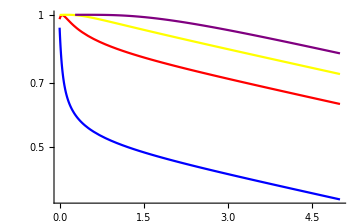

```mathematica
pp1=LogPlot[{ survival[2,t],survival[5,t], survival[10,t],survival[20,t]},{t,0,5},PlotStyle->{Blue,Red,Yellow,Purple},PlotRange->{All,{0,1}},ImageSize->Medium](*Note: x-axis is in units of seconds here*)
```

```mathematica
survivalProbData=Table[survival[2,t],{t,0.01,100,0.01}]; (*change 2 to other values for different values of z*)
Export["z2_k101_z202_term50.csv",survivalProbData]
```

Obtain the first-order term in the series solution

```mathematica
firstTermData1=Table[1.0273895467221033 HypergeometricU[-0.06470926953732073,3/2,0.012198067632850241 z^2],{z,1,100,0.01}];(* kappa=0.012*)
Export["ep_vs_firstTerm_kappa0.012.csv",firstTermData1]
```

ep_vs_firstTerm_kappa0.012.csv

```mathematica
firstTermData2=Table[HypergeometricU[-0.03175348022446587,3/2,0.0030495169082125602*z^2]*1.0158837275517005,{z,1,100,0.01}];(* kappa=0.003*)
Export["ep_vs_firstTerm_kappa0.003.csv",firstTermData2]
```

ep_vs_firstTerm_kappa0.003.csv

```mathematica
firstTermData3=Table[1.0105408582004236 HypergeometricU[-0.01994348955715985,3/2,0.0012198067632850243* z^2],{z,1,100,0.01}];(*kappa = 0.0012*)
Export["ep_vs_firstTerm_kappa0.0012.csv",firstTermData3]
```

ep_vs_firstTerm_kappa0.0012.csv

```mathematica
firstTermData4=Table[1.0035142808790085  HypergeometricU[-0.006255027713979893,3/2,0.00012198067632850242 z^2],{z,1,100,0.01}];(*kappa=0.00012*)
Export["ep_vs_firstTerm_kappa0.00012.csv",firstTermData4]
```

ep_vs_firstTerm_kappa0.00012.csv

Calculate and obtain the mean first-passage time (MFPT) using our series solution and using Grebenkov’s integral solution

```mathematica
termMFPT:=termMFPT=Table[weight[[m]]*myefs[[m]]/(2*myzeros[[m]]*kk/zeta),{m,1,mmax}]
```

```mathematica
MFPT[z_]=Total[termMFPT](*MFPT in infinite-sum form*)
```

-5.95789×10^-69 HypergeometricU[-49.4984,3/2,0.0121981 z^2]+3.13321×10^-67 HypergeometricU[-48.4934,3/2,0.0121981 z^2]-1.61583×10^-65 HypergeometricU[-47.4883,3/2,0.0121981 z^2]+8.1684×10^-64 HypergeometricU[-46.4832,3/2,0.0121981 z^2]-4.04614×10^-62 HypergeometricU[-45.4781,3/2,0.0121981 z^2]+1.963×10^-60 HypergeometricU[-44.4728,3/2,0.0121981 z^2]-9.32361×10^-59 HypergeometricU[-43.4675,3/2,0.0121981 z^2]+4.33342×10^-57 HypergeometricU[-42.4622,3/2,0.0121981 z^2]-1.96993×10^-55 HypergeometricU[-41.4568,3/2,0.0121981 z^2]+8.75441×10^-54 HypergeometricU[-40.4513,3/2,0.0121981 z^2]-3.80126×10^-52 HypergeometricU[-39.4458,3/2,0.0121981 z^2]+1.66308×10^-50 HypergeometricU[-38.4402,3/2,0.0121981 z^2]-6.67012×10^-49 HypergeometricU[-37.4345,3/2,0.0121981 z^2]+2.6923×10^-47 HypergeometricU[-36.4287,3/2,0.0121981 z^2]-1.05926×10^-45 HypergeometricU[-35.4229,3/2,0.0121981 z^2]+4.0596×10^-44 HypergeometricU[-34.417,3/2,0.0121981 z^2]-1.51444×10^-42 HypergeometricU[-33.411,3/2,0.0121981 z^2]+5.49528×10^-41 HypergeometricU[-32.4049,3/2,0.0121981 z^2]-1.93701×10^-39 HypergeometricU[-31.3987,3/2,0.0121981 z^2]+6.6369×10^-38 HypergeometricU[-30.3924,3/2,0.0121981 z^2]-2.20524×10^-36 HypergeometricU[-29.386,3/2,0.0121981 z^2]+7.10246×10^-35 HypergeometricU[-28.3795,3/2,0.0121981 z^2]-2.21509×10^-33 HypergeometricU[-27.3729,3/2,0.0121981 z^2]+6.68247×10^-32 HypergeometricU[-26.3661,3/2,0.0121981 z^2]-1.94784×10^-30 HypergeometricU[-25.3593,3/2,0.0121981 z^2]+5.47905×10^-29 HypergeometricU[-24.3523,3/2,0.0121981 z^2]-1.48535×10^-27 HypergeometricU[-23.3451,3/2,0.0121981 z^2]+3.87532×10^-26 HypergeometricU[-22.3378,3/2,0.0121981 z^2]-9.71597×10^-25 HypergeometricU[-21.3304,3/2,0.0121981 z^2]+2.33695×10^-23 HypergeometricU[-20.3228,3/2,0.0121981 z^2]-5.38303×10^-22 HypergeometricU[-19.315,3/2,0.0121981 z^2]+1.18516×10^-20 HypergeometricU[-18.3069,3/2,0.0121981 z^2]-2.48876×10^-19 HypergeometricU[-17.2987,3/2,0.0121981 z^2]+4.97329×10^-18 HypergeometricU[-16.2903,3/2,0.0121981 z^2]-9.43317×10^-17 HypergeometricU[-15.2815,3/2,0.0121981 z^2]+1.6936×10^-15 HypergeometricU[-14.2725,3/2,0.0121981 z^2]-2.86921×10^-14 HypergeometricU[-13.2632,3/2,0.0121981 z^2]+4.57108×10^-13 HypergeometricU[-12.2536,3/2,0.0121981 z^2]-6.82217×10^-12 HypergeometricU[-11.2435,3/2,0.0121981 z^2]+9.49781×10^-11 HypergeometricU[-10.233,3/2,0.0121981 z^2]-1.2276×10^-9 HypergeometricU[-9.22206,3/2,0.0121981 z^2]+1.46533×10^-8 HypergeometricU[-8.2105,3/2,0.0121981 z^2]-1.60605×10^-7 HypergeometricU[-7.19826,3/2,0.0121981 z^2]+1.60654×10^-6 HypergeometricU[-6.18521,3/2,0.0121981 z^2]-0.0000145836 HypergeometricU[-5.17115,3/2,0.0121981 z^2]+0.000119727 HypergeometricU[-4.15582,3/2,0.0121981 z^2]-0.000893461 HypergeometricU[-3.13878,3/2,0.0121981 z^2]+0.00628693 HypergeometricU[-2.1193,3/2,0.0121981 z^2]-0.0506471 HypergeometricU[-1.09592,3/2,0.0121981 z^2]+15.877 HypergeometricU[-0.0647093,3/2,0.0121981 z^2]

```mathematica
tauGreb[z_]:=Sqrt[Pi]*zeta/2/kk*{2*Sqrt[kappa]*NIntegrate[Exp[kappa*zz^2]*Erfc[Sqrt[kappa]*zz],{zz,1,z}]+Exp[kappa]*Erfc[Sqrt[kappa]]*kappa^{-1/2}-Exp[kappa*z^2]*Erfc[Sqrt[kappa]*z]*(kappa*z^2)^{-1/2}}(*MFPT in Grebenkov's integral form*)
```

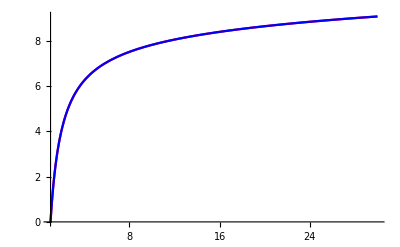

```mathematica
pp2=Plot[{MFPT[z]/(zeta/kk),tauGreb[z]/(zeta/kk)},{z,1,30},PlotStyle->{Red,Blue},PlotRange->All] (*Note: y-axis is in units of particle's relaxation time*)
```

```mathematica
data=Table[{MFPT[z]/(zeta/kk)},{z,1,30,0.01}];
Export["data.csv",data]
```

data.csv

```mathematica
dataGreb=Table[N[tauGreb[z]/(zeta/kk)],{z,1,30,.1}];
Export["dataGreb.csv",Flatten[dataGreb]]
```

dataGreb.csv